```mathematica
ClearAll["Global`*"]
NotebookDirectory[]
```

C:\Users\lenovo\source\repos\metvych_lab_5\metvych_lab_5\

```mathematica
data = {};
data =ReadList[StringJoin[NotebookDirectory[],"mass.txt"],Join[{Number},Table[Real,{i,1,2}]]];
```

```mathematica
n = data⟦1,1⟧;
```

```mathematica
data1 =Table[data⟦i,1⟧,{i,2,Length[data]}];
data2 = {};
dataLast = {};
For[j = 0, j<n, j++,
{For [i = 1, i ≤ n, i++,data2 = Append[data2, data1⟦i + j n⟧]];
dataLast = Append[dataLast, data2];
data2 = {};}
]
dataLast;
```

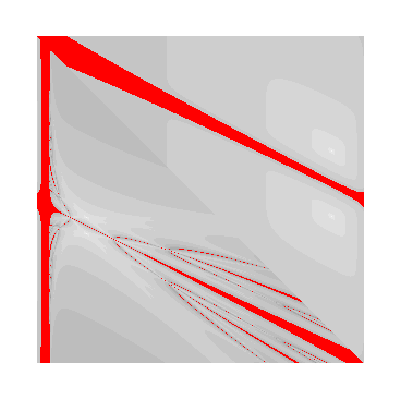

```mathematica
ArrayPlot[dataLast,ColorRules->{31->Red}]
```